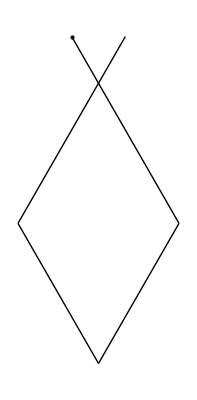

Show::gcomb: Could not combine the graphics objects in Show[{0,1},,,,].

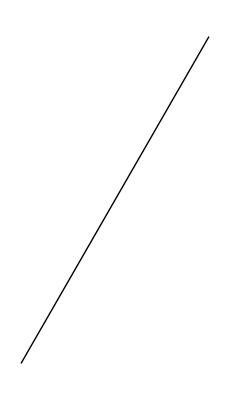
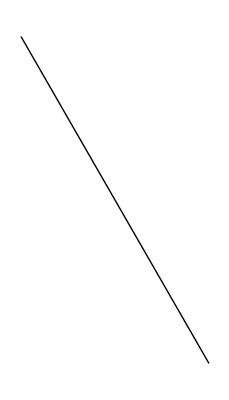
Show[{0,1},-Graphics-,-Graphics-,-Graphics-,-Graphics-]

```mathematica
(*deklaracja zmiennych*)
x:={4,3,3,4}
y:={1,2,3,4}
lista := {}
i:=1;
angle:=0;
startpoint={1,1};
endpoint={0,0};
(* tworzenie listy par liczb całkowitych *)
While[i<=4,AppendTo[lista,{x[[i]], y[[i]]}];i++]
(* rysujemy *)
points[1]=Graphics[Point[startpoint]];
For[i=1,i<=4,i++,
If[lista[[i]][[2]]== 1, angle:=60, If[lista[[i]][[2]]==2, angle:=120, If[lista[[i]][[2]]==3, angle:=240,If[lista[[i]][[2]]==4,angle:=300]]]];
endpoint[[1]]=startpoint[[1]] + lista[[i]][[1]] * Cos[angle Degree];
endpoint[[2]]=startpoint[[2]] - lista[[i]][[1]] * Sin[angle Degree];
line[i]=Graphics[Line[{startpoint,endpoint}]];
startpoint=endpoint
]
Show[points[1],line[1],line[2],line[3],line[4]]
```